```mathematica
f[x_]:=If[x==0,0,Exp[-1/x]]
g[x_]:=f[x]/(f[x]+f[1-x])
p={#,g[#]}&/@Range[0,1,0.1]
```

{{0.,0.},{0.1,0.000137894},{0.2,0.0229774},{0.3,0.12957},{0.4,0.302941},{0.5,0.5},{0.6,0.697059},{0.7,0.87043},{0.8,0.977023},{0.9,0.999862},{1.,1.}}

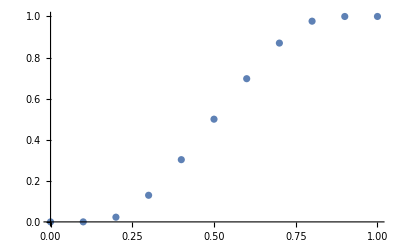

```mathematica
ListPlot[p]
```